ChemTools`DVR`Package

⌈Management⌋

$ChemDVRManager::usage="Manager interface for ChemDVR things";
ChemDVRDirectory::usage="Directory finder";
ChemDVRFile::usage=
	"Simple combination of FileNameJoin and ChemDVRDirectory";
ChemDVRPotentials::usage=
	"Lists all matching files in ChemDVRDirectory["PotentialEnergy"]";
$ChemDVRPotentials::usage="Alias for ChemDVRPotentials["*@.@*"]";

ChemDVRCreate::usage="OOP constructor for a ChemDVR";
ChemDVRAssociation::usage="Returns the base association for the instance";

ChemDVRSave::usage="Saves various ChemDVR components";
ChemDVRClear::usage="Clears saved ChemDVR components";

⌈Usage⌋

ChemDVRDimension::usage=
	"Returns the dimension of a ChemDVR object";

⌈Methods⌋

ChemDVRGrid::usage=
	"Returns the grid used in ChemDVR calculations";
ChemDVRKineticEnergy::usage=
	"Returns the kinetic energy used in ChemDVR calculations";
ChemDVRPotentialEnergy::usage=
	"Returns the potential energy used in ChemDVR calculations";
ChemDVRGridPotentialEnergy::usage=
		"Returns the potential energy used in ChemDVR calculations on the grid";
ChemDVRWavefunctions::usage=
	"Returns the wavefunctions computed in ChemDVR calculations";
ChemDVRGridWavefunctions::usage=
	"Returns the wavefunction imposed on the grid";
ChemDVRInterpolatingWavefunctions::usage=
	"Returns the wavefunctions interpolating over a grid";
ChemDVRExpectationValues::usage=
	"Returns the expectation values of a set of functions";
ChemDVROperatorMatrix::usage=
	"Returns the cross-state expectation matrix of a set of states->function specs";
ChemDVRView::usage="Displays the wavefunctions from a ChemDVR run";

⌈Interfaces⌋

ChemDVRNotebook::usage=
	"Opens a notebook for playing with a single ChemDVR instance";

Begin["`Private`"];

⌈Management⌋

⌈KeyWords⌋

$dvroot="Root";
$dvalt="ExtraDirs";
$dvrinst="Instances";
$dvrke="KineticEnergy";
$dvrpe="PotentialEnergy";
$dvrgp="GridPotentialEnergy";
$dvrwf="Wavefunctions";
$dvrgr="Grid";
$dvrgrwf="GridWavefunctions";
$dvrintwf="InterpolatingWavefunctions";
$dvrexv="ExpectationValues";
$dvrexm="OperatorMatrix";
$dvrvw="View";

⌈Manager⌋

If[!MatchQ[$ChemDVRManager,_Association],
	$ChemDVRManager=
		<|
			"Directories"→
				<|
					$dvroot→ChemExtensionDir["DVR"],
					$dvalt→
						Map[
							FileNameJoin[{#, "DVR"}]&,
							{$ChemExtensionsApp, $ChemExtensionsDev}
							],
					"Classes"→"Classes",
					$dvrinst→$dvrinst,
					$dvrpe→$dvrpe,
					$dvrke→$dvrke,
					$dvrwf→$dvrwf
					|>,
			"Objects"→
				<|
					|>,
			"Settings"→
				<|
					"Load"<>$dvrke→False,
					"Save"<>$dvrke→False,
					"Load"<>$dvrpe→False,
					"Save"<>$dvrpe→False,
					"Load"<>$dvrwf→False,
					"Save"<>$dvrwf→False
					|>
			|>
	];

⌈Directory⌋

$ChemDVRRoot:=
	$ChemDVRManager["Directories", $dvroot];
$ChemDVRPath:=
	Prepend[
		$ChemDVRManager["Directories", $dvalt],
		$ChemDVRRoot
		]

Options[ChemDVRDirectory]=
	{
		"Root":>$ChemDVRRoot,
		"Path":>$ChemDVRPath
		};
ChemDVRDirectory[
	dSpec_?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	alt:True|False:False,
	ops:OptionsPattern[]
	]:=
	With[{d=$ChemDVRManager["Directories", dSpec]},
		If[!alt,
			If[Not@DirectoryQ@ExpandFileName@d,
				(
					If[Not@DirectoryQ@#,
						CreateDirectory[#, CreateIntermediateDirectories→True]
						];
					#
					)&@
						FileNameJoin@{OptionValue["Root"], dSpec},
				d
				],
			FileNameJoin@{#,dSpec}&/@
				OptionValue["Path"]
			]
		];

⌈File⌋

ChemDVRFile//Clear

Options[ChemDVRFile]=
	Options@ChemDVRDirectory;
ChemDVRFile[
	dSpec_String?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	fspec__String,
	o:OptionsPattern[]
	]:=
	With[
		{
			ops=
				FileNameJoin@{#,fspec}&/@
					ChemDVRDirectory[dSpec, True, o]
			},
		SelectFirst[ops, FileExistsQ, Last@ops]
		];
ChemDVRFile[
	dSpec_String?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	ChemDVRObject[uuid_]
	]:=
	ChemDVRFile[
		dSpec,
		uuid<>If[MatchQ[dSpec,$dvrke|$dvrpe|$dvrwf],".mx",".m"]
		]
ChemDVRFile[ChemDVRObject[uuid_]]:=
	ChemDVRFile[$dvrinst,uuid<>".m"];

⌈Potentials⌋

ChemDVRPotentials[
	pat:_?StringPattern`StringPatternQ:"*@.@*",
	nameTake:True|False:True
	]:=
	If[nameTake,Map@FileNameTake,Identity]@
		FileNames[pat,ChemDVRDirectory[$dvrpe]];

⌈Create⌋

ChemDVRCreate::norng="No range function provided";
ChemDVRCreate::nogrid="No grid function provided";
ChemDVRCreate::noke="No kinetic energy function provided";
ChemDVRCreate::nope="No potential energy function provided";
ChemDVRCreate::novw="No view function provided";

ChemDVRCreate[a_Association]:=
	Block[{dvrAssoc=a},
		If[KeyMemberQ[a,"Class"],
			ChemDVRClass@a["Class"]];
		If[!KeyMemberQ[dvrAssoc,"UUID"],
			dvrAssoc["UUID"]=CreateUUID["ChemDVR-"]
			];
		If[!KeyMemberQ[dvrAssoc,"Name"],
			dvrAssoc["Name"]="ChemDVR Instance"
			];
		Map[
			If[!KeyExistsQ[dvrAssoc, #[[1]]],
				dvrAssoc[#[[1]]]=#[[2]]
				]&,
			{
				{$dvrgr, ChemDVRDefaultGrid},
				{$dvrke, ChemDVRDefaultKineticEnergy},
				{$dvrpe, ChemDVRDefaultPotentialEnergy},
				{$dvrgp, ChemDVRDefaultGridPotentialEnergy},
				{$dvrwf, ChemDVRDefaultWavefunctions},
				{$dvrvw, ChemDVRDefaultPlot},
				{$dvrgrwf, ChemDVRDefaultGridWavefunctions},
				{$dvrintwf, ChemDVRDefaultInterpolatingWavefunctions},
				{$dvrexv, ChemDVRDefaultExpectationValues},
				{$dvrexm, ChemDVRDefaultOperatorMatrix},
				{"FormatGrid", ChemDVRDefaultFormatGrid}
				}
			];
		$ChemDVRManager["Objects",dvrAssoc["UUID"]]=
			dvrAssoc;
		ChemDVRObject[dvrAssoc["UUID"]]
		];

ChemDVRCreate::nodvr="No ChemDVR found at ``";
ChemDVRCreate[dvr_String?FileExistsQ]:=
	With[{a=Get@dvr},
		If[AssociationQ@a,
			ChemDVRCreate@a,
			Message[ChemDVRCreate::nodvr,dvr];
			$Failed
			]
		];
ChemDVRCreate[dvr_String?(Not@*FileExistsQ)]:=
	With[{f=ChemDVRFile[$dvrinst,StringTrim[dvr,".m"]<>".m"]},	
		If[FileExistsQ@f,
			ChemDVRCreate@f,
			Message[ChemDVRCreate::nodvr,f]
			]
		];

⌈Save⌋

ChemDVRSave//Clear

Options[ChemDVRSave]=
	Options@ChemDVRFile;
ChemDVRSave[
	$dvrinst,
	name_String,
	a_Association,
	o:OptionsPattern[]
	]:=
	Block[{$ContextPath={"System`"}},
		Export[ChemDVRFile[$dvrinst, name, o],a]
		];
ChemDVRSave[
	prop:$dvrke|$dvrpe|$dvrwf, 
	name_String, 
	mx_List?MatrixQ,
	o:OptionsPattern[]
	]:=
	Export[	
		ChemDVRFile[prop, name, o],
		mx
		];

ChemDVRSave[
	Optional[$dvrinst,$dvrinst],
	ChemDVRObject[uuid_],
	o:OptionsPattern[]
	]:=
	ChemDVRSave[
		$dvrinst,
		uuid<>".m",
		$ChemDVRManager["Objects",uuid],
		o
		];
ChemDVRSave[
	prop:$dvrke|$dvrpe|$dvrwf, 
	ChemDVRObject[uuid_],
	mx_List?MatrixQ,
	o:OptionsPattern[]
	]:=
	ChemDVRSave[
		prop,
		uuid<>".mx",
		mx,
		o
		];

⌈Clear⌋

Options[ChemDVRClear]=
	Options@ChemDVRFile;
ChemDVRClear[prop:$dvrinst|$dvrke|$dvrpe|$dvrwf, name_String,
	ops:OptionsPattern[]
	]:=
	Quiet@DeleteFile@ChemDVRFile[prop,name, ops];

ChemDVRClear[
	prop:$dvrinst|$dvrke|$dvrpe|$dvrwf,$dvrinst,
	ChemDVRObject[uuid_],
	ops:OptionsPattern[]
	]:=
	ChemDVRClear[prop,
		uuid<>".m",
		ops
		];

⌈ChemDVRObject⌋

⌈Helpers⌋

chemDVRValidQ[uuid_String]:=
	KeyMemberQ[$ChemDVRManager["Objects"],uuid];
chemDVRValidQ[ChemDVRObject[uuid_]]:=
	chemDVRValidQ[uuid];
chemDVRValidQ[___]:=False;
dvrObjPattern=ChemDVRObject[uuid_?chemDVRValidQ]

dvrOpsLookup[ops___,key_,default_]:=
	Lookup[Flatten@Normal@{ops},key,default]
dvrOpsLookup~SetAttributes~HoldAll;

⌈Reloading⌋

ChemDVRObject//Clear

ChemDVRObject[a_Association]:=
	ChemDVRCreate[a];
ChemDVRObject[uuid_String?(
	Not@KeyMemberQ[$ChemDVRManager["Objects"],#]&&
		FileExistsQ@ChemDVRFile[$dvrinst, #<>".m"]
	&)]:=
	ChemDVRCreate[uuid];
ChemDVRObject[
	s_String?(
		Quiet@MatchQ[ChemDVRClass[#], ChemDVRClass[_Association?AssociationQ]]&
		), 
	o___?OptionQ
	]:=
	ChemDVRClass[s][o];

⌈Association⌋

ChemDVRAssociation[obj:dvrObjPattern]:=
	$ChemDVRManager["Objects",First@obj];

⌈Get⌋

ChemDVRGet[obj:dvrObjPattern,attribute_]:=
	Lookup[$ChemDVRManager["Objects",First@obj],attribute];
ChemDVRGet[obj:dvrObjPattern,attribute_,default_]:=
	Lookup[$ChemDVRManager["Objects",First@obj],attribute,default];

ChemDVRGet[obj:ChemDVRClass[a_Association],attribute_]:=
	Lookup[a,attribute];
ChemDVRGet[obj:ChemDVRClass[a_Association],attribute_,default_]:=
	Lookup[a,attribute,default];

PackageAddAutocompletions[
	ChemDVRGet,
	{
		None,
		{
			$dvrgr,
			$dvrke,$dvrpe,
			$dvrwf,$dvrgrwf,
			$dvrintwf,$dvrexv,
			$dvrexm,$dvrvw
			}
		}
	]

⌈Mutate⌋

ChemDVRMutate//ClearAll
ChemDVRMutate~SetAttributes~HoldAll;
With[{obPat=dvrObjPattern},
	ChemDVRMutate[(obj:obPat)[at___], fn_, args___]:=
		With[{k=First@obj},
			fn[
				$ChemDVRManager["Objects", k, at],
				args
				]
			];
	ChemDVRMutate[(obj:obPat)[[at___]], fn_, args___]:=
		With[{k=First@obj},
			fn[
				$ChemDVRManager[["Objects", k, at]],
				args
				]
			]
		];

⌈Set⌋

ChemDVRSet//Clear

ChemDVRSet[obj:dvrObjPattern, attribute__, value_]:=
	ChemDVRMutate[
		obj[attribute],
		Set,
		value
		]

⌈Options⌋

ChemDVROptions[obj:dvrObjPattern, method_String]:=
	Options@ChemDVRGet[obj, method];
ChemDVROptions[obj:dvrObjPattern, methods:{__String}]:=
	AssociationMap[ChemDVROptions[obj,#]&, methods];
ChemDVROptions[obj:dvrObjPattern, Optional[All, All]]:=
	ChemDVROptions[obj, 
		{$dvrgr, $dvrke, "PotentialEnergy", $dvrwf, "View"}
		]

PackageAddAutocompletions[
	ChemDVROptions,
	{
		None,
		{
			$dvrgr,
			$dvrke, $dvrpe, $dvrwf,
			$dvrvw
			}
		}
	]

⌈Dimension⌋

ChemDVRDimension[obj:dvrObjPattern]:=
	Length@ChemDVRGet[obj,"Range"];

⌈Grid⌋

ChemDVRRun::baddom=""Range" `` isn't a valid DVR domain specification";
ChemDVRRun::baddiv=""Points" `` isn't valid DVR division specification ";

ChemDVRGrid[obj:dvrObjPattern, ops:OptionsPattern[]]:=
	Block[{
		RunRange=None,
		RunPoints=None
		},
		RunRange=
			Replace[dvrOpsLookup[ops, "Range", None],
				l:{_?NumericQ,_?NumericQ}:>{l}
				];
		If[MatchQ[RunRange,{{_?NumericQ,_?NumericQ}..}],
			ChemDVRSet[obj,"Range",RunRange]
			];
		RunRange=ChemDVRGet[obj, "Range"];
		If[!MatchQ[RunRange,{{_?NumericQ,_?NumericQ}..}],
			Message[ChemDVRRun::baddom, RunRange];
			Throw[$Failed];
			];
		RunPoints=
			Replace[dvrOpsLookup[ops, "Points", None],
				l:_?IntegerQ:>{l}
				];
		If[MatchQ[RunPoints, {__?IntegerQ}],
			ChemDVRSet[obj, "Points", RunPoints]
			];
		RunPoints=ChemDVRGet[obj, "Points"];
		If[!MatchQ[RunPoints, {__?IntegerQ}],
			Message[ChemDVRRun::baddiv, RunPoints];
			Throw[$Failed];
			];
		ChemDVRGet[obj,"FormatGrid",(#&)][
			ChemDVRGet[obj,$dvrgr][
				RunPoints,
				RunRange,
				Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrgr]]
				],
			RunPoints
			]
		];

⌈KineticEnergy⌋

dvrCalcKE[obj_,ops___]:=
	With[{g=dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]]},
		ChemDVRGet[obj,$dvrke][g,Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrke]]]
		]

ChemDVRKineticEnergy[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{dvrke=ChemDVRGet[obj,$dvrke]},
		If[StringQ@dvrke,
			If[FileExistsQ@dvrke,Import@dvrke,Import@ChemDVRFile[$dvrke,dvrke]],
			With[{tryLoad=
				TrueQ@dvrOpsLookup[ops,"Load"<>$dvrke,
						dvrOpsLookup[ops,"Load",
							$ChemDVRManager["Settings","Load"<>$dvrke]]
						]},
				If[tryLoad,
					If[FileExistsQ@ChemDVRFile[$dvrke,obj],
						Import@ChemDVRFile[$dvrke,obj],
						ChemDVRKineticEnergy[obj,
							"Load"<>$dvrke→False,
							"Load"→False,
							ops
							]
						],
					With[{ke=dvrCalcKE[obj,ops]},
						If[MatrixQ[ke],
							If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrke,
									dvrOpsLookup[ops,"Save",
										$ChemDVRManager["Settings","Save"<>$dvrke]]
									],
								ChemDVRSave[$dvrke,obj,ke]
								]
							];
						ke
						]
					]
				]
			]
		];

⌈PotentialEnergy⌋

⌈dvrCalcPE⌋

dvrCalcPE[obj_,ops___]:=
	With[{g=dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]]},
		ChemDVRGet[obj,$dvrpe][g,
			Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrpe]]
			]
		]

⌈dvrLoadPotential⌋

dvrLoadPotential[obj_,file_,ops___]:=
	DiagonalMatrix@
		Flatten[
			dvrImportAlignPotential[
				obj,
				With[{
					gBase=dvrOpsLookup[ops, $dvrgr,ChemDVRGrid[obj,ops]],
					dim=ChemDVRDimension[obj]
					},
					If[Dimensions[gBase[[1]]][[dim]]=!=dim,
						SelectFirst[
							gBase,
							With[{d2=Dimensions[#[[1]]]},
								Length[d2]>=dim&&d2[[dim]]===dim
								]&,
							Throw[$Failed]
							],
						gBase
						]
					],
				file,
				FilterRules[{ops},Options@dvrImportAlignPotential]
				]
			]

⌈Main⌋

ChemDVRPotentialEnergy[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{dvrpe=dvrOpsLookup[ops,$dvrpe,ChemDVRGet[obj,$dvrpe]]},
		If[StringQ@dvrpe,
			If[FileExistsQ@dvrpe,
				dvrLoadPotential[obj,dvrpe,ops],
				dvrLoadPotential[obj,ChemDVRFile[$dvrpe, dvrpe],ops]
				],
			With[{tryLoad=
				TrueQ@dvrOpsLookup[ops,"Load"<>$dvrpe,
						dvrOpsLookup[ops,"Load",
							$ChemDVRManager["Settings","Load"<>$dvrpe]]
						]},
				If[tryLoad,
					If[FileExistsQ@ChemDVRFile[$dvrpe,obj],
						dvrLoadPotential[obj,ChemDVRFile[$dvrpe,obj],ops],
						ChemDVRPotentialEnergy[obj,
							"Load"<>$dvrpe→False,
							"Load"→False,
							ops]
						],
					With[{pe=dvrCalcPE[obj,ops]},
						If[MatrixQ[pe],
							If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrpe,
									dvrOpsLookup[ops,"Save",
										$ChemDVRManager["Settings","Save"<>$dvrpe]]
									],
								ChemDVRSave[$dvrpe,obj,pe]
								]
							];
						pe
						]
					]
				]
			]
		];

⌈GridPotentialEnergy⌋

ChemDVRGridPotentialEnergy[
	obj:dvrObjPattern,
	ops:OptionsPattern[]
	]:=
	With[{gp=ChemDVRGet[obj, $dvrgp]},
		gp[
			dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrpe,
				ChemDVRPotentialEnergy[obj, ops]
				],
			FilterRules[{ops},
				Options@gp
				]
			]
		]

⌈Wavefunctions⌋

dvrCalcWFs[obj_,ops___]:=
	With[{
		ke=
			dvrOpsLookup[ops,
				$dvrke,
				ChemDVRKineticEnergy[obj,ops]
				],
		pe=
			dvrOpsLookup[ops,
				"PotentialEnergy",
				ChemDVRPotentialEnergy[obj,ops]
				],
		wf=ChemDVRGet[obj,$dvrwf]
		},
		wf[
			ke,
			pe,
			Sequence@@
				FilterRules[{ops},
					Options@wf]
					]
		];

ChemDVRWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{tryLoad=
		TrueQ@dvrOpsLookup[ops,"Load"<>$dvrwf,
			dvrOpsLookup[ops,"Load",
				$ChemDVRManager["Settings","Load"<>$dvrwf]]
			]},
		If[tryLoad,
			If[FileExistsQ@ChemDVRFile[$dvrwf,obj],
				Import@ChemDVRFile[$dvrwf,obj],
				ChemDVRWavefunctions[obj,
					"Load"<>$dvrwf→False,
					"Load"→False,
					ops
					]
				],
			With[{wf=dvrCalcWFs[obj,ops]},
				If[Length@wf==2&&MatrixQ[Last@wf,NumericQ],
					If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrwf,
							dvrOpsLookup[ops,"Save",
								$ChemDVRManager["Settings","Save"<>$dvrwf]]
							],
						ChemDVRSave[$dvrwf,obj,wf]
						]
					];
				wf
				]
			]
		];

⌈GridWavefunctions⌋

ChemDVRGridWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{gridwf=ChemDVRGet[obj,$dvrgrwf]},
		gridwf[
			dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			FilterRules[{ops},
				Options@gridwf
				]
			]
		]

⌈InterpolatingWavefunctions⌋

ChemDVRInterpolatingWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{interpf=ChemDVRGet[obj, $dvrintwf]},
		interpf[
			dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			FilterRules[{ops},
				Options@interpf
				]
			]
		]

⌈ExpectationValues⌋

ChemDVRExpectationValues[
	obj:dvrObjPattern, 
	efuns:Except[_?OptionQ], 
	ops:OptionsPattern[]
	]:=
	With[{exFun=ChemDVRGet[obj, $dvrexv]},
		exFun[
			dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			efuns,
			FilterRules[{ops},
				Options@exFun
				]
			]
		]

⌈OperatorMatrix⌋

ChemDVROperatorMatrix[
	obj:dvrObjPattern, 
	efuns:Except[_?OptionQ], 
	ops:OptionsPattern[]
	]:=
	With[{exFun=ChemDVRGet[obj, $dvrexm]},
		exFun[
			dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			efuns,
			FilterRules[{ops},
				Options@exFun
				]
			]
		]

⌈View⌋

ChemDVRView[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{g=
		dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]]},
		With[{pe=
			dvrOpsLookup[ops,"PotentialEnergy",
				ChemDVRPotentialEnergy[obj,$dvrgr→g,ops]]},
			With[{wfs=
				dvrOpsLookup[ops,
					$dvrwf,
					ChemDVRWavefunctions[obj,
						$dvrgr→g,
						"PotentialEnergy"→pe,
						ops
						]
					]},
					ChemDVRGet[obj,"View"][wfs,g,pe,
						{ops}
						]
				]
			]
		]

⌈Run⌋

ChemDVRRun::badops="Options `` aren't valid for ChemDVRRun (OptionQ failed)"

⌈iChemDVRGetRuntimeOptions⌋

iChemDVRGetRuntimeOptions[keys__String]:=
	Sequence@@Normal@
		Fold[
			KeyDrop[
				Merge[
					{
						dvrOpsLookup[
							{#}, 
							#2<>"Options",
							{}
							],
						#
						},
					First
					],
				#2<>"Options"
				]&,
			Flatten@{RunRuntimeOptions},
			Reverse@{"Passed", keys}
			];

⌈iChemDVRRunHamiltonian⌋

iChemDVRRunHamiltonian[obj_]:=
	ChemDVRDefaultPrepareHamiltonian[
		Hold@RunKineticEnergy, 
		Hold@RunPotentialEnergy, 
		FilterRules[
			{iChemDVRGetRuntimeOptions[$dvrwf]}, 
			Options[ChemDVRDefaultPrepareHamiltonian]
			]
		];

⌈iChemDVRRunGridPotentialEnergy⌋

iChemDVRRunGridPotentialEnergy[obj_]:=
	ChemDVRGridPotentialEnergy[obj,
		$dvrgr→RunGrid,
		$dvrpe→RunPotentialEnergy,
		iChemDVRGetRuntimeOptions[$dvrgp, $dvrpe]
		];

⌈iChemDVRRunWavefunctions⌋

iChemDVRRunWavefunctions[obj_]:=
	ChemDVRWavefunctions[obj,
		$dvrke→
			If[ChemDVRGet[obj, "Wavefunctions"]===ChemDVRDefaultWavefunctions, 
				If[Head[RunKineticEnergy]===Hold,
					RunKineticEnergy,
					Hold[RunKineticEnergy]
					],
				RunKineticEnergy
				],
		$dvrpe→
			If[ChemDVRGet[obj, "Wavefunctions"]===ChemDVRDefaultWavefunctions, 
				If[Head[RunPotentialEnergy]===Hold,
					RunPotentialEnergy,
					Hold[RunPotentialEnergy]
					],
				RunPotentialEnergy
				],
		iChemDVRGetRuntimeOptions[$dvrwf]
		]

⌈iChemDVRRunEnergies⌋

iChemDVRRunEnergies[obj_]:=
	ChemDVRWavefunctions[obj,
		$dvrke→
			If[ChemDVRGet[obj, "Wavefunctions"]===ChemDVRDefaultWavefunctions, 
				If[Head[RunKineticEnergy]===Hold,
					RunKineticEnergy,
					Hold[RunKineticEnergy]
					],
				RunKineticEnergy
				],
		$dvrpe→
			If[ChemDVRGet[obj, "Wavefunctions"]===ChemDVRDefaultWavefunctions, 
				If[Head[RunPotentialEnergy]===Hold,
					RunPotentialEnergy,
					Hold[RunPotentialEnergy]
					],
				RunPotentialEnergy
				],
		"WavefunctionEigensolver"→Eigenvalues,
		iChemDVRGetRuntimeOptions[$dvrwf]
		]

⌈iChemDVRRunGridWavefunctions⌋

iChemDVRRunGridWavefunctions[obj_]:=
	ChemDVRGridWavefunctions[obj,
		$dvrwf→
			If[ChemDVRGet[obj, $dvrgrwf]===ChemDVRDefaultGridWavefunctions, 
				If[Head[RunWavefunctions]===Hold,
					RunWavefunctions,
					Hold[RunWavefunctions]
					],
				RunWavefunctions
				],
		$dvrgr→Hold@RunGrid,
		iChemDVRGetRuntimeOptions[$dvrgrwf, $dvrwf]
		];

⌈iChemDVRRunInterpolatingWavefunctions⌋

iChemDVRRunInterpolatingWavefunctions[obj_]:=
	ChemDVRInterpolatingWavefunctions[obj,
		$dvrwf→
			If[ChemDVRGet[obj, $dvrgrwf]===ChemDVRDefaultInterpolatingWavefunctions, 
				If[Head[RunWavefunctions]===Hold,
					RunWavefunctions,
					Hold[RunWavefunctions]
					],
				RunWavefunctions
				],
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrintwf]
		];

⌈iChemDVRRunExpectationValues⌋

iChemDVRRunExpectationValues[obj_]:=
	ChemDVRExpectationValues[obj,
		Replace[
			Rest@RunEndPoint,
			{
				{f:Except[_List]}:>f,
				e_:>Flatten[e]
				}
			],
		$dvrwf→
			If[ChemDVRGet[obj, $dvrgrwf]===ChemDVRDefaultExpectationValues, 
				If[Head[RunWavefunctions]===Hold,
					RunWavefunctions,
					Hold[RunWavefunctions]
					],
				RunWavefunctions
				],
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrexv]
		];

⌈iChemDVRRunOperatorMatrix⌋

iChemDVRRunOperatorMatrix[obj_]:=
	ChemDVROperatorMatrix[obj,
		Replace[
			Rest@RunEndPoint,
			{
				{f:Except[_List]}:>f,
				e_:>Flatten[e]
				}
			],
		$dvrwf→
			If[ChemDVRGet[obj, $dvrgrwf]===ChemDVRDefaultOperatorMatrix, 
				If[Head[RunWavefunctions]===Hold,
					RunWavefunctions,
					Hold[RunWavefunctions]
					],
				RunWavefunctions
				],
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrexm]
		]

⌈iChemDVRRun⌋

iChemDVRRun[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	Block[{
		RunObject=obj,
		RunRuntimeOptions=
			Sequence@@
				Normal@
					Merge[
						{
							"PassedOptions"→{ops},
							ChemDVRGet[obj, "RuntimeOptions", {}],
							ChemDVRGet[obj, "Defaults", {}],
							ops
							},
						First
						],
		RunCheckPoint=None,
		RunEndPoint,(*
		RunRange=None,
		RunPoints=None,*)
		RunGrid=None,
		RunTransformation=None,
		RunKineticEnergy=None,
		RunPotentialEnergy=None,
		RunWavefunctions=None
		},
		If[!OptionQ[{RunRuntimeOptions}], 
			Message[ChemDVRRun::badops, RunRuntimeOptions];
			Throw[$Failed]
			];
		RunEndPoint=
			dvrOpsLookup[RunRuntimeOptions, Return, "View"];
		If[dvrOpsLookup[RunRuntimeOptions, "Save", False],
			ChemDVRSave@obj
			];
		(*---------- Grid ---------*)
		RunGrid=dvrOpsLookup[RunRuntimeOptions, $dvrgr, None];
		If[RunGrid===None,
			RunGrid=
				ChemDVRGrid[obj,
					iChemDVRGetRuntimeOptions[$dvrgr]
					]
			];
		If[ListQ@RunGrid[[1]]&&SquareMatrixQ@RunGrid[[2]]&&!SquareMatrixQ[RunGrid[[1]]],
			{RunGrid, RunTransformation}=RunGrid
			];
		If[RunEndPoint===$dvrgr, Return@RunGrid];
		RunCheckPoint=$dvrgr;
		(*---------- Potential Optimization ---------*)
		If[RunEndPoint==="PotentialOptimization", 
			Return@
				ChemDVRDefaultPotentialOptimize[
					RunGrid,
					FilterRules[
						{
							iChemDVRGetRuntimeOptions[
								"PotentialOptimization",
								$dvrke,
								$dvrpe
								]
							},
						Options@ChemDVRDefaultPotentialOptimize
						]
					]
			];
		(*---------- Kinetic Energy ---------*)
		If[!MatchQ[RunEndPoint, $dvrpe|$dvrgr]&&
			!ListQ@dvrOpsLookup[RunRuntimeOptions, $dvrwf, None],
			RunKineticEnergy=
				dvrOpsLookup[RunRuntimeOptions, $dvrke, None];
			If[RunKineticEnergy===None,
				RunKineticEnergy=
					ChemDVRKineticEnergy[obj,
						$dvrgr→RunGrid,
						"TransformationMatrix"->RunTransformation,
						iChemDVRGetRuntimeOptions[$dvrke]
						]
				];
			];
		If[RunEndPoint===$dvrke, Return@RunKineticEnergy];
		RunCheckPoint=$dvrke;
		(*---------- Potential Energy ---------*)
		RunPotentialEnergy=
			dvrOpsLookup[RunRuntimeOptions, $dvrpe, None];
		If[RunPotentialEnergy===None,
			RunPotentialEnergy=
				ChemDVRPotentialEnergy[obj,
					$dvrgr→RunGrid,
					"TransformationMatrix"->RunTransformation,
					iChemDVRGetRuntimeOptions[$dvrpe]
					]
				];
		If[RunEndPoint===$dvrpe,Return@RunPotentialEnergy];
		RunCheckPoint=$dvrpe;
		(*---------- Grid Potential Energy ---------*)
		If[RunEndPoint===$dvrgp, 
			Return@iChemDVRRunGridPotentialEnergy[obj]];
		(*---------- Hamiltonian -----------*)
		If[RunEndPoint==="Hamiltonian", 
			Return[iChemDVRRunHamiltonian[obj]]
			];
		(*---------- Energies -----------*)
		If[RunEndPoint==="Energies", 
			Return@iChemDVRRunEnergies[obj]
			];
		(*---------- Wavefunctions ---------*)
		RunWavefunctions=
			dvrOpsLookup[RunRuntimeOptions, $dvrwf, None];
		If[RunWavefunctions===None,
			RunWavefunctions=iChemDVRRunWavefunctions[obj];
			];
		If[RunEndPoint===$dvrwf,
			Return@RunWavefunctions
			];
		RunCheckPoint=$dvrwf;
		(*---------- Rest -----------*)
		Switch[RunEndPoint,
			{
				(
					$dvrgr|$dvrke|$dvrpe|$dvrwf|"Hamiltonian"|"Energies"|
						$dvrgrwf|$dvrintwf|{$dvrexv, __}|{$dvrexm, __})..
				},
				Replace[
					Replace[
						DeleteDuplicates@RunEndPoint,
						{
							k:$dvrgr:>
								Block[{RunEndPoint=k},
									($dvrgr->RunGrid)
									],
							k:$dvrke:>
								Block[{RunEndPoint=k},
									($dvrke->RunKineticEnergy)
									],
							k:$dvrpe:>
									Block[{RunEndPoint=k},
										($dvrpe->RunPotentialEnergy)
										],
							k:$dvrwf:>
								Block[{RunEndPoint=k},
									($dvrwf->RunWavefunctions)
									],
							k:"Hamiltonian":>
								Block[{RunEndPoint=k},
									("Hamiltonian"->RunPotentialEnergy+RunKineticEnergy)
									],
							k:"Energies":>
								Block[{RunEndPoint=k},
									("Energies"->RunWavefunctions[[1]])
									],
							k:$dvrgrwf:>
								Block[{RunEndPoint=k},
									($dvrgrwf->iChemDVRRunGridWavefunctions[obj])
									],
							k:$dvrintwf:>
								Block[{RunEndPoint=k},
									($dvrintwf->iChemDVRRunInterpolatingWavefunctions[obj])
									],
							k:{$dvrexv, __}:>
								Block[{RunEndPoint=k},
									($dvrexv->iChemDVRRunExpectationValues[obj])
									],
							k:{$dvrexm, __}:>
								Block[{RunEndPoint=k},
									($dvrexm->iChemDVRRunOperatorMatrix[obj])
									]
							},
						1
						],
				o:{__Rule}:>Merge[o, Replace[{v_}:>v]]
				],
			$dvrgrwf,
				(*----------  Wavefunction Grid ---------*)
				iChemDVRRunGridWavefunctions[obj],
			$dvrintwf,
				(*----------  InterpolatingWavefunctions ---------*)
				iChemDVRRunInterpolatingWavefunctions[obj],
			{$dvrexv, __},
				(*----------  ExpectationValues ---------*)
				iChemDVRRunExpectationValues[obj],
			{$dvrexm, __},
				(*----------  Operator Matrix ---------*)
				iChemDVRRunOperatorMatrix[obj],
			"FullResults",
				If[ListQ@RunWavefunctions,
					<|
						"Grid"->
							If[ListQ@RunGrid, 
								RawArray["Real64", RunGrid],
								RunGrid
								],
						"PotentialEnergy"->
							If[ListQ@RunPotentialEnergy, 
								RawArray["Real64", RunPotentialEnergy],
								RunPotentialEnergy
								],
						"KineticEnergy"->
							If[ListQ@RunKineticEnergy, 
								RawArray["Real64", RunKineticEnergy],
								RunKineticEnergy
								],
						"Energies"->
							If[ListQ@RunWavefunctions, 
								RawArray["Real64", RunWavefunctions[[1]]],
								RunWavefunctions[[1]]
								],
						"Wavefunctions"->
							If[ListQ@RunWavefunctions, 
								RawArray["Real64", RunWavefunctions[[2]]],
								RunWavefunctions[[2]]
								]
						|>
					],
			_,
				(*---------- View ---------*)
				ChemDVRView[obj,
					$dvrwf→
						If[ChemDVRGet[obj, "View"]===ChemDVRDefaultPlot, 
							If[Head[RunWavefunctions]===Hold,
								RunWavefunctions,
								Hold[RunWavefunctions]
								],
							RunWavefunctions
							],
					$dvrpe→
						If[ChemDVRGet[obj, "View"]===ChemDVRDefaultPlot, 
							If[Head[RunPotentialEnergy]===Hold,
								RunPotentialEnergy,
								Hold[RunPotentialEnergy]
								],
							RunPotentialEnergy
							],
					$dvrgr→RunGrid,
					"TransformationMatrix"->RunTransformation,
					iChemDVRGetRuntimeOptions[$dvrvw]
					]
			]
		];

ChemDVRRun[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	Catch@With[{m=If[$Notebooks,dvrOpsLookup[ops,Monitor,False],False]},
		Switch[m,
			Automatic|True,	
				With[{start=Now,clock=Unique@"clock$"},
					Monitor[iChemDVRRun[obj, ops],
						With[{p=
							Replace[
								Position[
									{$dvrgr,$dvrke,$dvrpe,$dvrwf},
									RunCheckPoint
									],{
								{{i_}}:>i,
								_→-1
								}]},
							Panel@Grid[{
								{"Time Elapsed:",
									If[p<4,
										Row@{Dynamic[clock;Round[Now-start,.02]],
											Invisible@Pane[Animator[Dynamic@clock,{0,1,.1},1],{5,5}]},
										Now-start
										]},
								{"Grid:",If[p<1,"□","☑"]},
								{"Kinetic Energy:",If[p<2,"□","☑"]},
								{"Potential Energy:",If[p<3,"□","☑"]},
								{"Wavefunctions:",If[p<4,"□","☑"]}
								},
								Alignment→Left
								]
							]
						]
					],
			_Function,
				Monitor[iChemDVRRun[obj, ops], m@RunCheckPoint],
			_,
				iChemDVRRun[obj, ops]
			]
		];

⌈Notebook⌋

ChemDVRNotebook//Clear

Options[ChemDVRNotebook]=
	Join[
		{
			"SaveObject"→True
			},
		Options@Notebook
		];
ChemDVRNotebook[
	obj:dvrObjPattern,
	ops:OptionsPattern[]
	]:=
	With[
		{
			so=OptionValue["SaveObject"]
			},
		If[so,
			ChemDVRSave@obj
			];
		CreateDocument@
			Notebook[
				First@
					Get[PackageFilePath["Resources", "Templates", "DVRNotebook.nb"]],
				FilterRules[
					{
						ops,
						WindowTitle→ChemDVRGet[obj,"UUID"]
						},
					Options@Notebook
					]
				]
		]

⌈OOP Interface⌋

⌈Call⌋

$dvrBasicKeys=
	$dvrgr|$dvrpe|$dvrke|$dvrgp|
		$dvrwf|$dvrgrwf|$dvrintwf|
		"Hamiltonian"|"Energies"|"FullResults"|
		"PotentialOptimization";

ChemDVRObject[uuid_?chemDVRValidQ][a___?OptionQ]:=
	ChemDVRRun[ChemDVRObject[uuid],a];
(obj:_ChemDVRObject?chemDVRValidQ)[k:$dvrBasicKeys, args___?OptionQ]:=
	ChemDVRRun[obj, Return→k, args];
(obj:_ChemDVRObject?chemDVRValidQ)[k:$dvrexv|$dvrexm, 
		efuns:Except[_?OptionQ], args___?OptionQ]:=
	ChemDVRRun[obj, Return→{k, efuns}, args];
(obj:_ChemDVRObject?chemDVRValidQ)["Properties"]:=
	Keys@ChemDVRAssociation[obj];
(obj:_ChemDVRObject?chemDVRValidQ)["Association"]:=
	Keys@ChemDVRAssociation[obj];
(obj:_ChemDVRObject?chemDVRValidQ)["Options", thing___]:=
	ChemDVROptions[obj, thing];
(obj:_ChemDVRObject?chemDVRValidQ)[k:Except[_?OptionQ]..]:=
	ChemDVRGet[obj, k];
ChemDVRObject/:
	(obj:_ChemDVRObject?chemDVRValidQ)[[k:Except[_?OptionQ]..]]:=
		ChemDVRGet[obj, k];

⌈Mutate⌋

ChemDVRObjMutate//ClearAll;
ChemDVRObjMutate~SetAttributes~HoldAllComplete;
$ChemDVROneArgMutators=
	Set|SetDelayed|TimesBy|DivideBy|AddTo|SubtractFrom|
		PrependTo|AppendTo|AssociateTo|KeyDropFrom;
$ChemDVRBaseNoArgMutators=
	Increment|Decrement;
ChemDVRObject/:(m:Set|SetDelayed)[
	obj_ChemDVRObject?chemDVRValidQ[k:Except[_?OptionQ]..],
	v_]:=
	ChemDVRMutate[obj[k], m, v];
With[{oneArgs=$ChemDVROneArgMutators, noArg=$ChemDVRNoArgMutators},
	ChemDVRObjMutate[
		(m:oneArgs)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[k:Except[_?OptionQ]..],
			a_
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[k], m, a]
			];
	ChemDVRObjMutate[
		(m:oneArgs)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[[k:Except[_?OptionQ]..]],
			a_
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[[k]], m, a]
			];
	ChemDVRObjMutate[
		(m:noArg)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[k:Except[_?OptionQ]..]
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[k], m]
			];
	ChemDVRObjMutate[
		(m:noArg)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[[k:Except[_?OptionQ]..]]
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[[k]], m]
			];
		];

Language`SetMutationHandler[ChemDVRObject, ChemDVRObjMutate]

⌈Formatting⌋

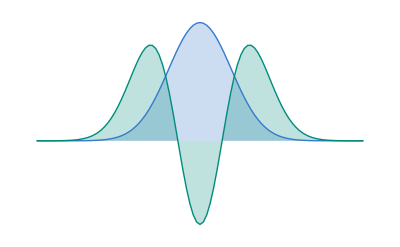
$dvrimg=
	Graphics[First@#,
		{
			ImageSize→{28,28},
			AspectRatio→Full,
			Method→{"ShrinkWrap"→True}
			}
		]&@-Graphics-;

Format[obj:dvrObjPattern?chemDVRValidQ]:=
	RawBoxes@
		BoxForm`ArrangeSummaryBox[
			"ChemDVRObject",
			obj,
			Replace[ChemDVRGet[obj,"Icon"],_Missing→$dvrimg],
				{
					BoxForm`MakeSummaryItem[{"Name: ",ChemDVRGet[obj,"Name"]},StandardForm],
					BoxForm`MakeSummaryItem[{"UUID: ",ChemDVRGet[obj,"UUID"]},StandardForm]
					},
			Block[{$ContextPath={"System`"}},
				Map[
					BoxForm`MakeSummaryItem[{Row@{#,": "},ChemDVRGet[obj,#]},StandardForm]&,{
						"Range",
						"Points",
						$dvrgr,
						$dvrke,
						$dvrpe,
						$dvrwf
					}]
				],
			StandardForm
			];

End[];